## Init

### Base

Set the Census API key

```mathematica
(*SystemCredential["USCensusAPIKey"]="your Census API key"*)
```

```mathematica
Options[censusQuery]={
Authentication:>SystemCredential["USCensusAPIKey"],
"APIBase"->"api.census.gov"
};
```

```mathematica
censusQuery[path_,query_,opts:OptionsPattern[]]:=
Enclose@Module[{rawResponse,responseList},
rawResponse=Confirm@URLRead@HTTPRequest[<|
"Scheme"->"HTTPS",
"Domain"->OptionValue["APIBase"],
"Path"->path,
"Query"->Join[
query,
{"key"->OptionValue[Authentication]}
]
|>];
responseList=Confirm[Import[rawResponse,"RawJSON"],rawResponse];
ToTabular[Rest@responseList,"Rows",<|"ColumnKeys"->First@responseList|>]
]
```

## Data

```mathematica
fipsCode=Entity["AdministrativeDivision",{"Georgia","UnitedStates"}][EntityProperty["AdministrativeDivision","FIPSCode"]]
```

13

### ACS Detail Tables

```mathematica
pathACS={"data","2022","acs","acs5"};
```

```mathematica
acsCategoriesCodes=<|
"WhiteAlone"->"A",
"BlackOrAfricanAmericanAlone"->"B",
"AsianAlone"->"D",
"AmericanIndianAndAlaskaNativeAlone"->"C",
"NativeHawaiianAndOtherPacificIslanderAlone"->"E",
"SomeOtherRaceAlone"->"F",
"TwoOrMore"->"G",
"HispanicOrLatino"->"I",
"WhiteAloneNotHispanicOrLatino"->"H",
"Overall"->""
|>;
```

```mathematica
getVAPVarsACS[r0_]:=
With[{r=Replace[r0,acsCategoriesCodes]},
{
"B05003"<>r<>"_008E",
"B05003"<>r<>"_019E"
}
]
getVAPVarsACS[r0_List]:=Union@@(getVAPVarsACS/@r0)
```

### PUMS

```mathematica
pathPUMS={"data","2022","acs","acs5","pums"};
```

```mathematica
varsPUMS={"PWGTP","CIT","AGEP","HISP","RACWHT","RACBLK","RACASN","RACAIAN","RACNH","RACPI","RACSOR","RACNUM"};
```

```mathematica
getVAPStatePUMSRaw[fipsCode_]:=
censusQuery[
pathPUMS,
{
"get"->StringRiffle[varsPUMS,","],
"for"->"state:"<>fipsCode
}
]
```

```mathematica
getVAPStatePUMS[fipsCode_]:=
Select[
ConstructColumns[getVAPStatePUMSRaw[fipsCode],
{
"PersonWeight"->Function[Cast[#PWGTP,"UnsignedInteger16"]],
"Age"->Function[Cast[#AGEP,"UnsignedInteger8"]],
"Citizen"->Function[#CIT=!="5"],
"HispanicOrLatino"->Function[#HISP=!="01"],
"White"->Function[#RACWHT==="1"],
"BlackOrAfricanAmerican"->Function[#RACBLK==="1"],
"Asian"->Function[#RACASN==="1"],
"AmericanIndianAndAlaskaNative"->Function[#RACAIAN==="1"],
"NativeHawaiianAndOtherPacificIslander"->Function[#RACNH==="1"||#RACPI==="1"],(*PUMS splits only this category into two variables for some reason*)
"SomeOtherRace"->Function[#RACSOR==="1"]
}
],
#Age>=18&
]
```

## Scratch space

```mathematica
raceEthnicityAxes={
"HispanicOrLatino",
"White",
"BlackOrAfricanAmerican",
"Asian",
"AmericanIndianAndAlaskaNative",
"NativeHawaiianAndOtherPacificIslander",
"SomeOtherRace"
};
```

```mathematica
pums=getVAPStatePUMS[fipsCode];
```

```mathematica
acs=CastColumns[
censusQuery[
pathACS,
{
"get"->StringRiffle[getVAPVarsACS[Keys[acsCategoriesCodes]],","],
"for"->"tract:*",
"in"->"county:*",
"in"->"state:"<>fipsCode
}
],
getVAPVarsACS[Keys[acsCategoriesCodes]]->"Integer"
];
```

```mathematica
geoids=Union@Normal@ConstructColumns[acs,"geoid"->Function[#state<>#county<>#tract]][[All,"geoid"]];
```

```mathematica
geoidIndices=PositionIndex[geoids][[All,1]];
```

```mathematica
raceEthnicityAxesIndices=PositionIndex[DeleteCases[Subsets[Sort@raceEthnicityAxes],{}|{"HispanicOrLatino"}]][[All,1]];
```

```mathematica
acsCategoriesIndices=Map[raceEthnicityAxesIndices@*Sort,<|
"WhiteAlone"->{{"White"},{"White","HispanicOrLatino"}},
"BlackOrAfricanAmericanAlone"->{{"BlackOrAfricanAmerican"},{"BlackOrAfricanAmerican","HispanicOrLatino"}},
"AsianAlone"->{{"Asian"},{"Asian","HispanicOrLatino"}},
"AmericanIndianAndAlaskaNativeAlone"->{{"AmericanIndianAndAlaskaNative"},{"AmericanIndianAndAlaskaNative","HispanicOrLatino"}},
"NativeHawaiianAndOtherPacificIslanderAlone"->{{"NativeHawaiianAndOtherPacificIslander"},{"NativeHawaiianAndOtherPacificIslander","HispanicOrLatino"}},
"SomeOtherRaceAlone"->{{"SomeOtherRace"},{"SomeOtherRace","HispanicOrLatino"}},
"TwoOrMore"->Catenate[{#,Union[#,{"HispanicOrLatino"}]}&/@Subsets[DeleteCases[raceEthnicityAxes,"HispanicOrLatino"],{2,Infinity}]],
"HispanicOrLatino"->(Union[#,{"HispanicOrLatino"}]&/@Subsets[DeleteCases[raceEthnicityAxes,"HispanicOrLatino"],{1,Infinity}]),
"WhiteAloneNotHispanicOrLatino"->{{"White"}}
|>,{2}];
```

```mathematica
marginalSets={};
```

```mathematica
KeyValueMap[
AppendTo[marginalSets,{{raceEthnicityAxesIndices@Sort@Pick[raceEthnicityAxes,#1]},Values@geoidIndices}->#2]&,
GroupBy[pums,Lookup[raceEthnicityAxes]->Lookup["PersonWeight"],Total]
];
```

```mathematica
Function[cat,
Module[{agg},
agg=ConstructColumns[acs,{
"v"->Function[Total@Lookup[#,getVAPVarsACS[cat]]],
"geoid"->Function[#state<>#county<>#tract]
}];
Scan[
AppendTo[marginalSets,{acsCategoriesIndices[cat],{geoidIndices[#geoid]}}->#v]&,
FromTabular[agg,"Rows"]
]
]
]/@Keys@acsCategoriesIndices;
```

```mathematica
sa=SparseArray[{},{Length@marginalSets,Length@raceEthnicityAxesIndices,Length@geoids}];
MapIndexed[sa[[First[#2],#1[[1,1]],#1[[1,2]]]]=1;&,marginalSets];
```

```mathematica
sa=;
```

```mathematica
saFlat=Transpose@Flatten[Transpose[sa,{3,2,1}],1];
```

```mathematica
saFlat
```

```mathematica
y=Values[marginalSets];
```

```mathematica
si=Lookup[GroupBy[saFlat["ExplicitPositions"],First->Last],Range[Length[saFlat]]];
```

```mathematica
psaFlat=SparseArray@PseudoInverse@N@saFlat;//EchoTiming
```

6.91555

```mathematica
psaFlat
```

SparseArray[…]

```mathematica
psa=ArrayReshape[Transpose@psaFlat,Dimensions@sa]
```

SparseArray[…]

```mathematica
xHat=psaFlat.y;
```

```mathematica
xHat=LeastSquares[N@saFlat,y];
```

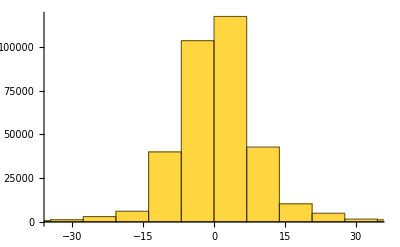

```mathematica
Histogram@xHat
```

```mathematica
Total[ArrayReshape[xHat,Dimensions[sa][[2;;]]][[acsCategoriesIndices["WhiteAlone"]]],2]
```

133689.

```mathematica
Total@Total@Normal@acs[[All,getVAPVarsACS["WhiteAlone"]]]
```

4632395

```mathematica
Total[xHat[[acsCategoriesIndices["WhiteAlone"]]]]
```

2242.79

```mathematica
a=saFlat;
```

```mathematica
(*sol=QuadraticOptimization[
Total[Inactive[Subtract][Inactive[Dot][a,x],y]^2,Infinity],
{x\[VectorGreaterEqual]0},
x∈Vectors[Dimensions[a][[2]],Integers]
];//EchoTiming*)
```

```mathematica
Beep[]
```

```mathematica
sol1=ConvexOptimization[
Total@Abs@Inactive[Subtract][Inactive[Dot][a,x],y],
{},
x∈Vectors[Dimensions[a][[2]],NonNegativeIntegers],
Method->"MOSEK"
];//EchoTiming
```

18.4082

```mathematica
Beep[]
```

```mathematica
sol2=ConvexOptimization[
Total@Abs@Inactive[Subtract][Inactive[Dot][a,x],y],
{},
x∈Vectors[Dimensions[a][[2]],NonNegativeReals],
Method->"MOSEK"
];//EchoTiming
```

11.2671

```mathematica
Beep[]
```

```mathematica
(*sol3=ConvexOptimization[
Total[Inactive[Power][Inactive[Subtract][Inactive[Dot][a,x],y],2]],
{},
x∈Vectors[Dimensions[a][[2]],NonNegativeReals],
Method->"MOSEK"
];//EchoTiming*)
```

```mathematica
sol3=ConvexOptimization[
Inactive[Norm][Inactive[Subtract][Inactive[Dot][a,x],y]],
{},
x∈Vectors[Dimensions[a][[2]],NonNegativeReals],
Method->"MOSEK"
];//EchoTiming
```

9.94354

```mathematica
Beep[]
```

```mathematica
(*sol4=ConvexOptimization[
Inactive[Norm][Inactive[Subtract][Inactive[Dot][a,x],y]],
{},
x∈Vectors[Dimensions[a][[2]],NonNegativeIntegers],
Method->"MOSEK"
];//EchoTiming*)
```

```mathematica
Beep[]
```

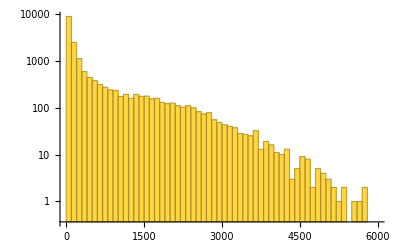

```mathematica
Histogram[DeleteCases[x/.sol1,0],Automatic,{"Log","Count"},PlotRange->{{0,6000},All}]
```

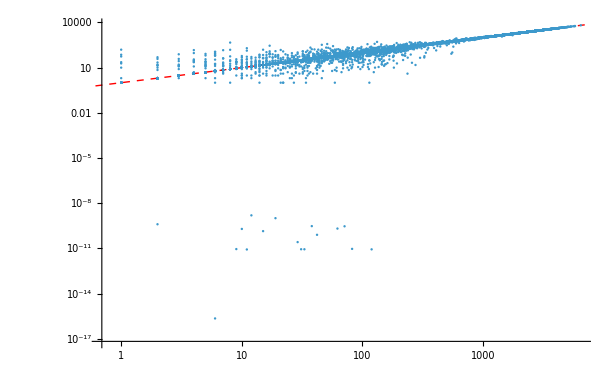

```mathematica
ListLogLogPlot[Transpose[{x/.sol1,x/.sol2}],Epilog->{Red,Dashed,InfiniteLine[{0,0},{1,1}]}]
```

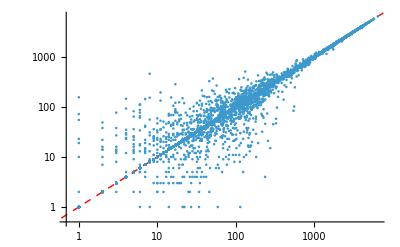

```mathematica
ListLogLogPlot[Transpose[{x/.sol1,Round[x/.sol2]}],Epilog->{Red,Dashed,InfiniteLine[{0,0},{1,1}]}]
```

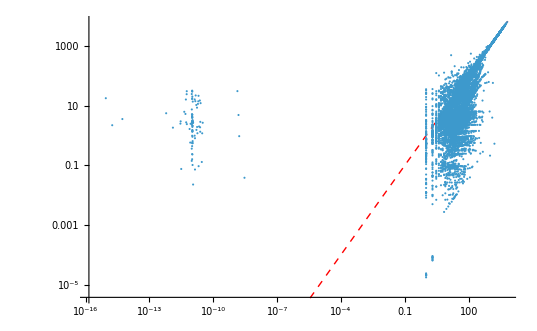

```mathematica
ListLogLogPlot[Transpose[{x/.sol2,x/.sol3}],Epilog->{Red,Dashed,InfiniteLine[{0,0},{1,1}]}]
```

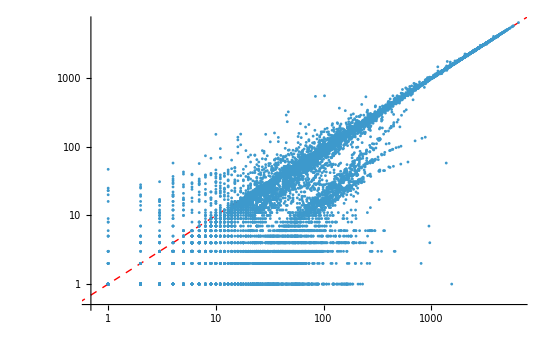

```mathematica
ListLogLogPlot[Transpose[Round@{x/.sol2,x/.sol3}],Epilog->{Red,Dashed,InfiniteLine[{0,0},{1,1}]}]
```

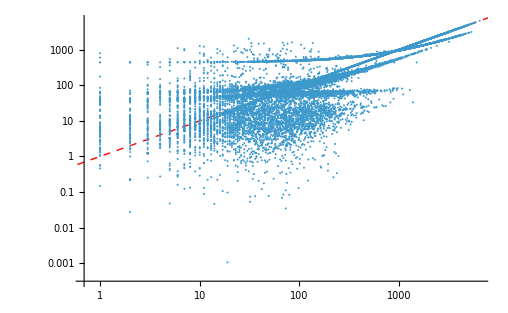

```mathematica
ListLogLogPlot[Transpose[{x/.sol1,xHat}],Epilog->{Red,Dashed,InfiniteLine[{0,0},{1,1}]}]
```

### Min-max

```mathematica
solMin=ConvexOptimization[
Inactive[Total][Abs[Inactive[Subtract][Inactive[Times][a[[All,6]],x],y]]],
{},
x∈NonNegativeIntegers,
Method->"MOSEK"
];//EchoTiming
```

0.068321

```mathematica
xRangeAt[a_,y_,k_]:=Module[{n,obj,sol,opt,minSol,maxSol},n=Dimensions[a][[2]];
obj=Total@Abs@Inactive[Subtract][Inactive[Dot][a,x],y];
sol=ConvexOptimization[obj,{},x∈Vectors[n,NonNegativeIntegers],Method->"MOSEK"];
Echo["solved main"];
opt=Activate[obj/.sol];
Echo[opt];
minSol=Echo@ConvexOptimization[Indexed[x,k],{obj==opt},x∈Vectors[n,NonNegativeIntegers],Method->"MOSEK"];
maxSol=Echo@ConvexOptimization[-Indexed[x,k],{obj==opt},x∈Vectors[n,NonNegativeIntegers],Method->"MOSEK"];
<|"OptimalObjectiveValue"->opt,"Min"->Activate[obj/.minSol],"Max"->-Activate[obj/.maxSol],"MinSolution"->minSol,"MaxSolution"->maxSol|>]
```

```mathematica
Beep[]
```

### Normal-normal

```mathematica
{m,n}=Dimensions[saFlat][[;;2]]
```

{25261,352296}

```mathematica
mu0=ConstantArray[100,n];
sigma0=100.*IdentityMatrix@n;
ySigma=5;
```

```mathematica
sigma0Inv=(*Inverse[sigma0]*)1/100.*IdentityMatrix@n;
```

```mathematica
(*sigma=Inverse[sigma0Inv+(1/ySigma^2) Transpose[saFlat].saFlat];*)
mu=ySigma*(sigma0Inv.mu0+(1/ySigma^2) Transpose[saFlat].y);
```

```mathematica
mu
```

```mathematica
Length@y
```

25261

```mathematica
Dimensions[sa][[2]]
```

126

```mathematica
saFlat
```

SparseArray[<802452>, {25261, 352296}]

```mathematica
Total@Total@Normal@acs[[All,getVAPVarsACS["WhiteAlone"]]]
```

4632395

```mathematica
Total[mu[[acsCategoriesIndices["WhiteAlone"]]]]
```

927191.

$Aborted